# Wolfram/CodeEquivalenceUtilities

Utilities for testing code equivalence

## Paclet Manifest

"Data"

"Documentation"

"English"

"Guides"

"CodeEquivalenceUtilities.nb"DocumentationEnglishGuidesCodeEquivalenceUtilities.nb

"ReferencePages"

"Symbols"

"CodeEquivalentQ.nb"DocumentationEnglishReferencePagesSymbolsCodeEquivalentQ.nb

"EquivalenceTestData.nb"DocumentationEnglishReferencePagesSymbolsEquivalenceTestData.nb

"FromCanonicalForm.nb"DocumentationEnglishReferencePagesSymbolsFromCanonicalForm.nb

"MakeCanonicalForm.nb"DocumentationEnglishReferencePagesSymbolsMakeCanonicalForm.nb

"ToCanonicalForm.nb"DocumentationEnglishReferencePagesSymbolsToCanonicalForm.nb

"$AllowedEvaluationPatterns.nb"DocumentationEnglishReferencePagesSymbols$AllowedEvaluationPatterns.nb

"Tutorials"

"AddingNewTransformationRules.nb"DocumentationEnglishTutorialsAddingNewTransformationRules.nb

"Images"

"0bf8dc73177c188f.png"Images0bf8dc73177c188f.png

"0d12d8551029ee6a.png"Images0d12d8551029ee6a.png

"12a4ebc788f8cb2c.png"Images12a4ebc788f8cb2c.png

"152f8d1bb9acf613.png"Images152f8d1bb9acf613.png

"1cd67b7d1f0771ae.png"Images1cd67b7d1f0771ae.png

"267c2baf6dadcfcc.png"Images267c2baf6dadcfcc.png

"3a38f3a85d4a4795.png"Images3a38f3a85d4a4795.png

"43a40f076b9b5860.png"Images43a40f076b9b5860.png

"52714167c1555ca8.png"Images52714167c1555ca8.png

"58724d56ad2d0a5d.png"Images58724d56ad2d0a5d.png

"59eada987ec4d919.png"Images59eada987ec4d919.png

"5dfbd7b1ec4305fe.png"Images5dfbd7b1ec4305fe.png

"674eb267f6beef39.png"Images674eb267f6beef39.png

"751d18c398c2d8f2.png"Images751d18c398c2d8f2.png

"hero-image.png"Imageshero-image.png

"Kernel"

"64Bit"

"CodeEquivalenceUtilities.mx"Kernel64BitCodeEquivalenceUtilities.mx

"CachedValues.wl"KernelCachedValues.wl

"CanonicalForms"

"Attributes.wl"KernelCanonicalFormsAttributes.wl

"Common.wl"KernelCanonicalFormsCommon.wl

"ExperimentalRules.wl"KernelCanonicalFormsExperimentalRules.wl

"Graphics.wl"KernelCanonicalFormsGraphics.wl

"Rules.wl"KernelCanonicalFormsRules.wl

"Scope.wl"KernelCanonicalFormsScope.wl

"Structural.wl"KernelCanonicalFormsStructural.wl

"CodeEquivalenceUtilities.wl"KernelCodeEquivalenceUtilities.wl

"Config.wl"KernelConfig.wl

"Debugging.wl"KernelDebugging.wl

"Equivalence.wl"KernelEquivalence.wl

"EvaluationControl.wl"KernelEvaluationControl.wl

"Formatting.wl"KernelFormatting.wl

"Legacy.wl"KernelLegacy.wl

"Types.wl"KernelTypes.wl

"Utilities.wl"KernelUtilities.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

"Scripts"

"BuildAssets.wls"ScriptsBuildAssets.wls

"BuildMX.wls"ScriptsBuildMX.wls

"CreateWorkflows.wls"ScriptsCreateWorkflows.wls

"FormatNotebooks.wls"ScriptsFormatNotebooks.wls

"TestPaclet.wls"ScriptsTestPaclet.wls

"TestReport.wls"ScriptsTestReport.wls

"Tests"

"AllowedEvaluationPatterns.wlt"TestsAllowedEvaluationPatterns.wlt

"Attributes.wlt"TestsAttributes.wlt

"Common.wlt"TestsCommon.wlt

"Data"

"EIWLData.wl"TestsDataEIWLData.wl

"EIWL.wlt"TestsEIWL.wlt

"EvaluationControl.wlt"TestsEvaluationControl.wlt

"Misc.wlt"TestsMisc.wlt

"QuestionFramework.wlt"TestsQuestionFramework.wlt

"Rules.wlt"TestsRules.wlt

## Web Content

### Headline Image

```mathematica
graph=Graph[{
a->x,
b->x,
a1->a,
a11->a1,
a12->a1,
a2->a,
a22->a2,
b1->b,
b2->b
},
EdgeStyle->Directive[Thickness[.03],GrayLevel[.85],Arrowheads[.15],Opacity[1]],
VertexSize->Medium,
VertexStyle->Directive[GrayLevel[.85],EdgeForm[None],Opacity[1]],
ImageSize->500,
AspectRatio->1
];
img=Show[HighlightGraph[graph,{Style[PathGraph[FindShortestPath[graph,b2,x],DirectedEdges->True],ColorData[97][1]],Style[PathGraph[FindShortestPath[graph,a22,x],DirectedEdges->True],ColorData[97][2]],
Style[x,ColorData[97][3]]},VertexLabels->{b2->Placed[Framed[Style[Defer@f[…],FontColor->ColorData[97][1],FontSize->36,FontWeight->Bold],Background->White,RoundingRadius->8,FrameMargins->8,FrameStyle->Directive[Thickness[5],ColorData[97][1]]],Center],a22->Placed[Framed[Style[Defer@g[…],FontColor->ColorData[97][2],FontSize->36,FontWeight->Bold],Background->White,RoundingRadius->8,FrameMargins->8,FrameStyle->Directive[Thickness[5],ColorData[97][2]]],Center],
x->Placed[Style["✓",FontWeight->Bold,FontSize->150,FontColor->ColorData[97][3]],{3.5,1.5}]
}],ImageSize->450,AspectRatio->1]/.{HoldPattern[f]->RawBoxes["f"],HoldPattern[g]->RawBoxes["g"],HoldPattern[…]->RawBoxes["…"]};
ImagePad[ImageCrop@Rasterize[img,ImageResolution->144,Background->None],{{0,100},{0,0}},None]
```

-Graphics-

### Basic Description

CodeEquivalenceUtilities is a collection of Wolfram Language functions that can be used to test if different pieces of code are equivalent without the need for evaluation.

This allows comparison of unevaluated expressions that may have non-deterministic outputs (e.g. random values, dates, etc).

This Paclet represents the underlying technology that powers several automated code grading systems, such as the online exercises for EIWL and Wolfram Challenges.

### Details

TODO

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
Get[FileNameJoin[{NotebookDirectory[],"Scripts","BuildMX.wls"}]];
$CachePersistence="Session";
```

### Basic Examples

Check if two expressions are equivalent:

```mathematica
CodeEquivalentQ[RandomInteger/@Range[5],Array[RandomInteger,5]]
```

True

View the canonical representations of expressions:

```mathematica
MakeCanonicalForm[RandomInteger/@Range[5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

```mathematica
MakeCanonicalForm[Array[RandomInteger,5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

These are directly comparable:

```mathematica
%===%%
```

True

### Scope

Get additional information about the equivalence test:

```mathematica
EquivalenceTestData[
First[Rest[Range/@Range[2^100]]],
Part[Table[Table[j,{j,i}],{i,2^100}],2]
]
```

<|Timing→<|SameQ→0.,ToCanonicalForm1→1.432998,ToCanonicalForm2→2.202002|>,SameQ→False,CanonicalForms→<|1→HoldComplete[Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,1267650600228229401496703205376,1}]⟦2⟧],2→HoldComplete[Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,1267650600228229401496703205376,1}]⟦2⟧]|>,CanonicalEquivalentQ→True,EquivalentQ→True|>

View the sequence of transformations used to convert an expression to its canonical form:

```mathematica
MakeCanonicalForm[Array[RandomInteger,5],"Trace"->True]//Column
```

Array[RandomInteger,5]
Table[RandomInteger[S1],{S1,5}]
Table[RandomInteger[S1],{S1,1,5,1}]
Table[RandomInteger[S1∷ℤ],{S1∷ℤ,1,5,1}]
Table[RandomInteger[{0,S1∷ℤ}],{S1∷ℤ,1,5,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

Convert a canonical representation to a normal expression:

```mathematica
MakeCanonicalForm[Array[RandomInteger,5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,5,1}]

```mathematica
FromCanonicalForm[%]
```

Table[RandomVariate[DiscreteUniformDistribution[{0,S1}]],{S1,1,5,1}]

Evaluate:

```mathematica
ReleaseHold[%]
```

{0,1,2,0,4}

### Neat Examples

Here is a list of expressions, some of which are equivalent to others:

```mathematica
expressions={
HoldForm[Table[i,{i,5},{j,i+2}]],
HoldForm[Array[Range,5,3]],
HoldForm[Table[ConstantArray[i,i+2],{i,5}]],
HoldForm[First[Rest[Range/@Range[10]]]],
HoldForm[Range/@Range[3,7]],
HoldForm[Part[Table[Table[j,{j,i}],{i,10}],2]]
};
```

Find the sequence of transformations for each expression:

```mathematica
Short[traces=Most@ToCanonicalForm[#,"Trace"->True]&/@expressions]
```

{{Table[i,{i,5},{j,i+2}],Table[Table[S1,{S2,S1+2}],{S1,5}],«4»,Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]},«4»,{«1»}}

Generate a graph for each sequence:

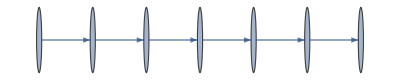
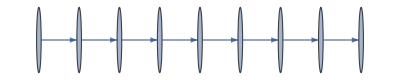
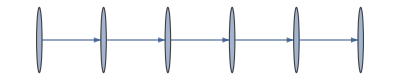
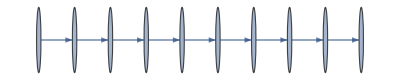
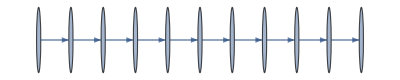
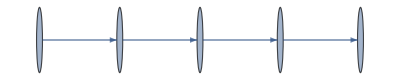

```mathematica
paths=Graph[DirectedEdge@@@Partition[#,2,1]]&/@traces
```

Combine the graphs:

```mathematica
graph=Graph[GraphUnion@@paths,];
```

Equivalent expressions converge to the same connected component:

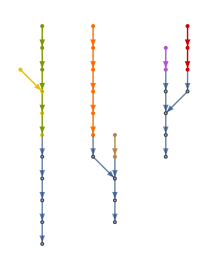

```mathematica
HighlightGraph[graph,paths]
```

Group the expressions into their corresponding equivalence class:

```mathematica
grouped=GroupBy[expressions,ToCanonicalForm]
```

<|Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]→{Table[i,{i,5},{j,i+2}],Table[ConstantArray[i,i+2],{i,5}]},Table[Table[S1∷ℤ,{S1∷ℤ,1,2+S2∷ℤ,1}],{S2∷ℤ,1,5,1}]→{Array[Range,5,3],Range/@Range[3,7]},Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,10,1}]⟦2⟧→{First[Rest[Range/@Range[10]]],Table[Table[j,{j,i}],{i,10}]⟦2⟧}|>

```mathematica
TableForm[KeyValueMap[Reverse@*List,grouped]]
```

Table[i,{i,5},{j,i+2}]
Table[ConstantArray[i,i+2],{i,5}] | Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]
Array[Range,5,3]
Range/@Range[3,7] | Table[Table[S1∷ℤ,{S1∷ℤ,1,2+S2∷ℤ,1}],{S2∷ℤ,1,5,1}]
First[Rest[Range/@Range[10]]]
Table[Table[j,{j,i}],{i,10}]⟦2⟧ | Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,10,1}]⟦2⟧

## Source & Additional Information

### Creator

Richard Hennigan <richardh@wolfram.com>

### Source Control Repository

https://github.com/rhennigan/CodeEquivalenceUtilities

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

canonical forms

code comparison

code transformations

education

equality

equivalence

code grading

intension

metaprogramming

type theory

wolfram language

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

SameExpressionShapeQ

SameInstanceQ

SameAsQ

CheckMatch

DefinitionData

EvaluationTiming

ExpressionLineDiff

ReplaceContext

### Original Source References and Attributions

Source, reference or citation information

### Links

Wolfram Videos - Determining Code Equivalence for Automated Grading

Wolfram Videos - Wolfram Challenges: Behind the Scenes

Wolfram Challenges: Programming Puzzles for the Wolfram Language

An Elementary Introduction to the Wolfram Language - Online Exercises

### Compatibility

#### Wolfram Language Version

12.2+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies <+$Path+>, <+Directory+>, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public <+ResourceObject+> content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of <+SystemCredential+>Click for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via <+ExternalEvaluate+>
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.